# Probability Distributions of Discrete Random Variables

In our previous discussion of probability distributions, we focus on developing the rules of probability. Now, we will learn about discrete probability distributions. For a discrete random variable, the probabilities of values are areas of the corresponding regions of the probability histogram for the variable.

## Discrete Probability Distribution

The word random here means that the outcomes are uncertain in the short run but have a regular distribution or predictable pattern in the long run. In statistics, we reserve the term random variable for quantitative variables.

Example: Consider the random variable, X, the number of times a student changes major. Here is the probability distribution of the random variable X:

```mathematica
associaToGrid[data_]:=
{Join[{"x"},Part[Transpose[List@@@Normal@KeySort@(Counts@data)],1]],Join[{"P(x)"},Part[Transpose[List@@@Normal@KeySort@(Counts@data)],2]/Length[data]//N]}
```

```mathematica
data=RandomVariate[PoissonDistribution[2],100];
Labeled[Grid[associaToGrid[data],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],{Rotate["Prob",90 Degree],"The Number of Times Major Changed"},{Left,Top}]
```

x | 0 | 1 | 2 | 3 | 4 | 5 | 6
P(x) | 0.1 | 0.34 | 0.28 | 0.15 | 0.1 | 0.02 | 0.01ProbThe Number of Times Major Changed

```mathematica
(*data={Table[0,135],Table[1,271],Table[2,271],Table[3,180],Table[4,90],Table[5,36],Table[6,12],Table[7,3],Table[8,2]};
data=Flatten[data];*)
```

A discrete probability distribution is a list of all the possible values of the discrete random variable together with each value’s probability. Each probability is between 0 and 1, and the sum of all probabilities is 1.

Another way to represent the probability distribution of a random variable is with a probability histogram.

What is the sum of the heights of the bars?

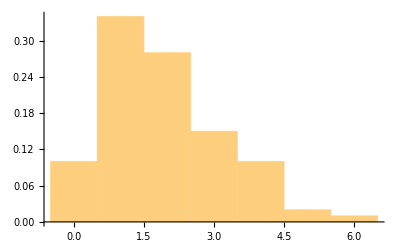
-Graphics-ProbabilityThe Number of Times Major Changed

```mathematica
Labeled[Histogram[data,Automatic,"Probability"],{Rotate[
   "Probability", 90 Degree], "The Number of Times Major Changed"}, {Left, Bottom}]
```

What is the shape of this probability histogram? What does the histogram shape suggest to you about the number of times a student changes major?

Imagine that we select one student at random. Find the probability that the student changes major at most four times.

Find the probability that the student changes major more than five times.

Find the probability that the student changes major between two and four times, inclusive.

Now imagine that we randomly select three students. What is the probability that all three students change their major more than five times? Assume that each student is independent from the others.

Using the histogram, estimate the mean number of times major changed. Think about the shape of the distribution and remember that the mean doesn’t have to be a whole number.

### Mean of Discrete Probability Distribution

The mean of a probability distribution represents both the average value of the random variable and the center of the distribution. Since a value with a large probability occurs more frequently than a value with a low probability, the calculation of the mean must include each value’s probability. The formula below shows that the mean is found by

multiplying each value by its probability, then

adding these products together.

μ = ∑ x·P(x)

The mean is also referred to as the expected value.

Calculate the mean number of times the number of times a student changes major.

```mathematica
Labeled[Grid[Insert[associaToGrid[data],Join[{"xP(x)"}, Table["                 ",7]],{3}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],{Rotate["Mean",90 Degree],"The Number of Times Major Changed"},{Left,Top}]
```

x | 0 | 1 | 2 | 3 | 4 | 5 | 6
P(x) | 0.1 | 0.34 | 0.28 | 0.15 | 0.1 | 0.02 | 0.01
xP(x) |                   |                   |                   |                   |                   |                   |                  MeanThe Number of Times Major Changed

The mean of a discrete random variable is also called the expected value. What does this tell us in the context of this problem?

### Standard Deviation of Discrete Probability Distribution

The standard deviation of a discrete probability distribution is given by

σ = √(∑ (x-μ)^2·P(x))

Calculate the standard deviation of the probability distribution for the number of times a student changes major

```mathematica
Labeled[Grid[Insert[associaToGrid[data],Table["                 ",8],{3}],Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],{Rotate["Std. Dev.",90 Degree],"The Number of Times Major Changed"},{Left,Top}]
```

x | 0 | 1 | 2 | 3 | 4 | 5 | 6
P(x) | 0.1 | 0.34 | 0.28 | 0.15 | 0.1 | 0.02 | 0.01
                  |                   |                   |                   |                   |                   |                   |                  Std. Dev.The Number of Times Major Changed

How do you interpret this standard deviation?

### Probability and Area

Let’s explore the relationship between probability and area. In the previous probability histogram, the 
width of each bar in the histogram is 1.

What is the area of the bar centered at 1?

What is the area of the bar centered at 2?

What is the relationship between a value’s area and its probability?

What is the sum of the areas of all the bars?

### Example

At BHCC, there have been complaints about how long it takes to get food from the college cafeteria. In response, a study was conducted to record the total amount of time students had to wait to get their food. The following table gives the total times (rounded to the nearest 5 minutes) to get food for 200 randomly selected students.

```mathematica
data2={{"Wait Time in Minutes",5,10,15,20,25},{"Number of Students",30,52,62,40,16}};
Labeled[Grid[data2,Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"],{"Cafeteria Wait Times"},{Top}]
```

Wait Time in Minutes | 5 | 10 | 15 | 20 | 25
Number of Students | 30 | 52 | 62 | 40 | 16Cafeteria Wait Times

Using this data, create a probability distribution for the random variable X = “time to get food.”

Calculate the expected wait time for students to get their food in the cafeteria.

Calculate the standard deviation of the wait time for students to get their food in the cafeteria.

What is the probability that a student will wait for less than 15 minutes?

## Exercises

Ling just moved to Boston and is paying $1.70 each time she takes the bus. During a typical month she does not take many trips, so she does not really want to waste money to buy a monthly bus pass for $55. Since you are a statistics student, you decide to help her make a probability distribution for the number of  times she take the bus each month. The results are in the following histogram:

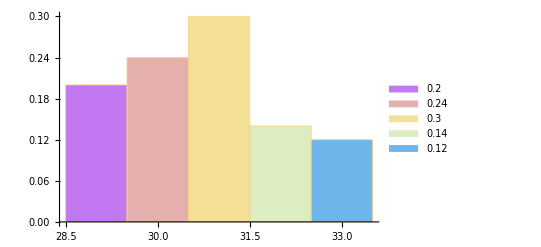

```mathematica
data3=Join[Table[29,20],Table[30,24],Table[31,30],Table[32,14],Table[33,12]];
elements=Part[Transpose[List@@@Normal@(Counts@data3)],2]/Length[data3]//N;
Histogram[data3,Automatic,"Probability",ChartStyle->"Pastel",ChartLegends->elements]
(* Mean[data3]//N *)
```

Should Ling order the monthly pass or keep paying for each bus ride separately? Use the mean of the distribution to answer your question.

Authorship information

Jie Frye

June 30, 2017

jiefrye@gmail.com